```mathematica
phi:=0.7
mu:=0.1
chi:=0.6
alpha:=0.9
kappa:= 0.2
De:=2.9
Dpl:=1.3
Dpg:=2.3
Dil:=1.7
Dig:=2.9
psi:=0.95
```

{{0,0,0.7 b,0.1 b,0.7 b,0.1 b,0.07 b,0.01 b},{0,0,0.1 b,0.6 b,0.1 b,0.6 b,0.01 b,0.06 b},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

{{0.344828,0,0,0,0,0,0,0},{0,0.344828,0,0,0,0,0,0},{-0.344828,0,0.668673,0,0,0,0,0},{0,-0.344828,0,0.668673,0,0,0,0},{0,0,-0.584615,0,0.588235,0,0,0},{0,0,0,-0.584615,0,0.588235,0,0},{0,0,-0.0173913,0,0,0,0.344828,0},{0,0,0,-0.0173913,0,0,0,0.344828}}

{{2.9,0.,0.,0.,0.,0.,0.,0.},{0.,2.9,0.,0.,0.,0.,0.,0.},{1.4955,0.,1.4955,0.,0.,0.,0.,0.},{0.,1.4955,0.,1.4955,0.,0.,0.,0.},{1.4863,0.,1.4863,0.,1.7,0.,0.,0.},{0.,1.4863,0.,1.4863,0.,1.7,0.,0.},{0.0754251,0.,0.0754251,0.,0.,0.,2.9,0.},{0.,0.0754251,0.,0.0754251,0.,0.,0.,2.9}}

{2.27729 bet,1.60885 bet,0.,0.,0.,0.,0.,0.}

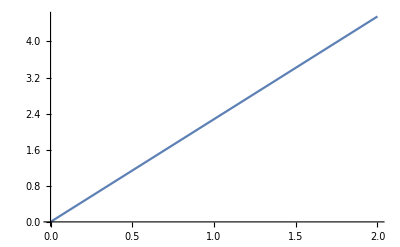

```mathematica
F[b_]=b*{{0,0, phi,mu ,phi, mu , phi*(1-alpha), mu*(1-alpha)},
{0,0, mu, chi, mu, chi, mu*(1-alpha), chi*(1-alpha)},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0}
}

v={{1/De,0,0,0,0,0,0,0},
{0,1/De,0,0,0,0,0,0},
{-1/De, 0, (1-kappa)*psi/Dpl+(1-kappa)*(1-psi)/Dpg+kappa/(Dpl+Dil),  0,0,0,0,0},
{0,-1/De, 0, (1-kappa)*psi/Dpl+(1-kappa)*(1-psi)/Dpg+kappa/(Dpl+Dil), 0,0,0,0},
{0,0,-(1-kappa)*psi/Dpl, 0,1/Dil,0,0,0},
{0,0,0,-(1-kappa)*psi/Dpl, 0,1/Dil,0,0},
{0,0,-(1-kappa)*(1-psi)/Dpg, 0,0,0,1/Dig,0},
{0,0,0,-(1-kappa)*(1-psi)/Dpg,  0,0,0,1/Dig}}
mV=Inverse[v]
eig[bet_]=Eigenvalues[F[bet].mV]
R0[bet_]:=Part[eig[bet],1]
Plot[R0[x],{x,0,2}]
```